# Predicting Climate risks

## Exploratory Data Analysis

## Data Loading & Cleaning

### Data Loading

```mathematica
ds = Import["/Users/jeannefernandez/Desktop/E4S_Master/MA3/Data science & ML II/Project/predicting-climate-risks/data/dataset_sample.csv", "Dataset", "HeaderLines" -> 1];
(*Import dataset sample*)
```

```mathematica
RandomSample[ds, 5]
```

### Data Cleaning

```mathematica
ds = KeyDrop[{""}]@ds; (*Drop emtpy column*)
ds = ds[All,KeyMap[Replace[{"Ultimate Parent Name"->"Company", "Ultimate Parent ISIN"->"ISIN","ExposureScore_Composite_ModerateHigh_2020" -> "Risk2020",
"ExposureScore_Composite_ModerateHigh_2030" -> "Risk2030","ExposureScore_Composite_ModerateHigh_2040" -> "Risk2040","ExposureScore_Composite_ModerateHigh_2050" -> "Risk2050","ExposureScore_Composite_ModerateHigh_2060" ->"Risk2060",
"ExposureScore_Composite_ModerateHigh_2070" -> "Risk2070","ExposureScore_Composite_ModerateHigh_2080" -> "Risk2080",
"ExposureScore_Composite_ModerateHigh_2090"-> "Risk2090"}]]];(*Rename columns name*)
RandomSample[ds, 5];
```

### Integral Score

Our goal it to give a summary of the risk approximation by decade into one scalar statistic, called Integral Score. 
We first visualise several options for this score, given the risk values by decade.
One can fit a function given the risk approximation for several years, and then integrate the resulting curve.
The choice of score then boils down to the choice of approximation.

{62,63,62,60,62,59,59,63}

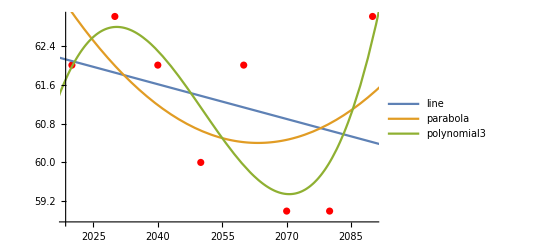

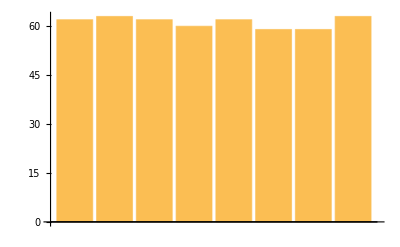

Linear approximation (line): 4890.48

Quardatic approximation (parabola): 4894.29

Third degree approximation (polynomial3): 4923.98

Rectangle approximation (barchart): 4900

```mathematica
x = {2020, 2030, 2040,2050,2060,2070, 2080, 2090};
yRandom = Normal@Values@RandomSample[ds[All, {7;;14}],1][[1,1]] (*We pick one row at random to illustrate all the possible scores*)
data = Transpose@Normal@{x,yRandom};
line = Fit[data, {1,z}, z];
parabola = Fit[data, {1,z,z^2}, z];
polynomial3 = Fit[data, {1,z,z^2,z^3}, z];
Show[ListPlot[data,PlotStyle->Red],Plot[{line, parabola, polynomial3},{z,2010,2100}, PlotLegends->"Expressions"]]
BarChart[yRandom]
Print["Linear approximation (line): ", Integrate[line,{z,2020,2100}]]
Print["Quardatic approximation (parabola): ",Integrate[parabola,{z,2020,2100}]]
Print["Third degree approximation (polynomial3): ",Integrate[polynomial3,{z,2020,2100}]]
Print["Rectangle approximation (barchart): ",(Total@yRandom)*10]
```

We note that all the approximations are in the same order of magnitude. For the sake of simplicity and to avoid overfitting, we choose the linear approximation. We add the chosen Integral Score to the dataset.

```mathematica
intColumn =ds[All,<|"integralScore"->Integrate[
Fit[Transpose@Normal@{x,{#Risk2020,#Risk2030,#Risk2040,#Risk2050,#Risk2060,#Risk2070,#Risk2080,#Risk2090}}, {1,z}, z]
,{z,2020,2100}]|>&];
```

```mathematica
dataset=Join[ds,intColumn,2];
RandomSample[dataset, 5]
```